# ClO2-I-MA oscillations

Chlorine Dioxide-Iodine-Malonic Acid

Lengyel, Rabai, Epstein
"Experimental and Modeling Study of Oscillations in the
Chlorine Dioxide-Iodine-Malonic Acid Reaction"
Journal of the Am. Chem. Soc. (1990) 112:9104-9110

implemented 24 Oct 09 B.E.S.
LGPL license terms apply

```mathematica
<<xlr8r.m
```

xlr8r 0.74 (13 May 2009) loaded 25 October 2009 at 10:22 GMT-06:60 using Mathematica 7.0 for Linux x86 (64-bit) (February 18, 2009) (Version 7., Release 1) (MathSBML 2.9.0 [8-Oct-2008])
GNU Lesser General Public License (LGPL) Terms Apply.

### This is the published (simplified) network

referfence equations 5,6
The basic scheme is the following 5th order modification of the standard Lotka system:
	A→X
	X→Y
	4X + Y →P with kXY/(μ+X^2)

#### Build and run the Cellerator Model

```mathematica
net={{∅-> X, k1}, {X-> Y, k2}, 
{4 X+Y-> ∅, (k3/X[t]^3)/(1+X[t]^2)}
};
interpret[net][[1]]//TableForm
```

X'[t]==k1-k2 X[t]-(4 k3 X[t] Y[t])/(1+X[t]^2)
Y'[t]==k2 X[t]-(k3 X[t] Y[t])/(1+X[t]^2)

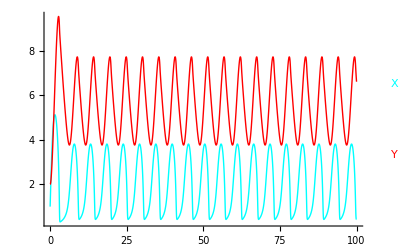

```mathematica
n=run[net//.{k1-> 10,  k2-> 1, k3->1}, initialConditions-> {X-> 1, Y-> 2}];
runPlot[n]
```

#### Save CelleratorML file

```mathematica
<<CelleratorML.m
```

Cellzilla2D (2.1.α.18 5 Sept 2009) loaded Sun 25 Oct 2009 10:23:00 using xlr8r 0.74 (13 May 2009) and xSSA 1.1.α.5 (23-Jul-2009)

CelleratorML 1.0.5 (19 June 2009) loaded 25 October 2009 at 10:23 GMT-06:60 using Mathematica Version 7.0 for Linux x86 (64-bit) (February 18, 2009) Release 1

```mathematica
SaveModel["Lengyel-Reduced.xml", net, "InitialConditions"-> {X-> 1, Y-> 2}, 
"Parameters"-> {k1-> 10, k2-> 1, k3-> 1}, 
"Model"-> "ClO2-I-MA"]
```

Lengyel-Reduced.xml

Model: Model4

CelleratorML Version: 1.0

3 reactions

3 parameters

2 initial values

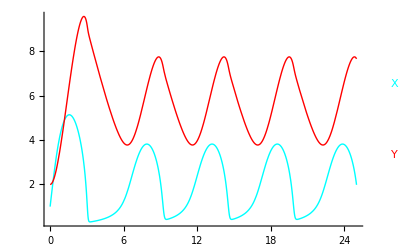

```mathematica
{model, parms, iv, opts}=GetModel["Lengyel-Reduced.xml"]; 
run[model, initialConditions-> iv, rates-> parms, timeSpan-> 25]; 
runPlot[%]
```

### Try to modify it to remove the 5th order reaction

The rate constants in this modification are not consistent with the original model. This is for demonstration purposes only.

#### Build and run the modified model

X'[t]==k1-k2 X[t]-kdx X[t]+kr X3Y[t]-(kf X[t] X3Y[t])/(1+X[t]^2)+kr X4Y[t]+kr XXY[t]-(kf X[t] XXY[t])/(1+X[t]^2)+kr XY[t]-(kf X[t] XY[t])/(1+X[t]^2)+kdy Y[t]-(kf X[t] Y[t])/(1+X[t]^2)
X3Y'[t]==-kr X3Y[t]-(kf X[t] X3Y[t])/(1+X[t]^2)+kr X4Y[t]+(kf X[t] XXY[t])/(1+X[t]^2)
X4Y'[t]==(kf X[t] X3Y[t])/(1+X[t]^2)-kr X4Y[t]
XXY'[t]==kr X3Y[t]-kr XXY[t]-(kf X[t] XXY[t])/(1+X[t]^2)+(kf X[t] XY[t])/(1+X[t]^2)
XY'[t]==kr XXY[t]-kr XY[t]-(kf X[t] XY[t])/(1+X[t]^2)+(kf X[t] Y[t])/(1+X[t]^2)
Y'[t]==k2 X[t]+kr XY[t]-kdy Y[t]-(kf X[t] Y[t])/(1+X[t]^2)

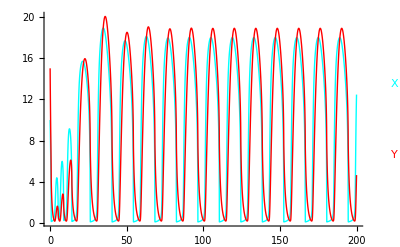

```mathematica
netm={{∅⇄ X, k1, kdx}, {X⇄ Y, k2 ,kdy},
{X+Y⇄ XY, kf/(1+X[t]^2), kr}, {X+XY⇄ XXY, kf/(1+X[t]^2), kr}, {X+XXY⇄ X3Y,kf/(1+X[t]^2), kr}, 
{X+X3Y⇄ X4Y, kf/(1+X[t]^2), kr}
};
Print[interpret[netm][[1]]//TableForm]

n=run[netm//.{k1-> 10,  k2-> 1, k3->1, kf-> 10, kr-> 1, kdy-> 1, kdx-> 1}, initialConditions-> {X-> 10, Y-> 15, XY-> 0, XXY-> 0, X3Y-> 0, X4Y-> 0}, timeSpan-> 200, MaxSteps-> 100000];
runPlot[n, {X,Y}]
```

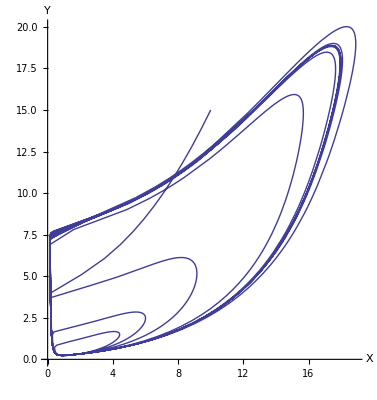

```mathematica
PhasePlot[n, {X, Y}, {0, 200}]
```

#### Save XML of modified model

```mathematica
SaveModel["Lengyel-Modified.xml", netm,  "InitialConditions"-> {X-> 1, Y-> 2, XY-> 0, XXY-> 0, X3Y-> 0, X4Y-> 0}, 
"Parameters"-> {k1-> 10,  k2-> 1, k3->1, kf-> 10, kr-> 1, kdy-> 1, kdx-> 1}, 
"Model"-> "ClO2-I-MA-Modified"]
```

Lengyel-Modified.xml

Model: Model7

CelleratorML Version: 1.0

6 reactions

7 parameters

6 initial values

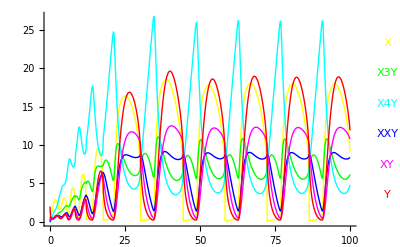

```mathematica
{model, parms, iv, opts}=GetModel["Lengyel-Modified.xml"]; 
run[model, initialConditions-> iv, rates-> parms, timeSpan-> 100]; 
runPlot[%]
```